Name : Soy Vitou                   Class : ITE-G8-A

find Exact value

```mathematica
DSolve[{y'[x]==1+y[x],y[0]==1},y[x],x]
```

{{y[x]→-1+2 ⅇ^x}}

```mathematica
y[x]/.{{y[x]->-1+2 ⅇ^x}}
```

{-1+2 ⅇ^x}

```mathematica
yxact[x_] := -1+ⅇ^x*2
```

initialize first value

```mathematica
x[a_,b_,n_,0]:= 0
```

```mathematica
y[a_,b_,n_,0]:= 1
```

find f(x, y)

```mathematica
f[a_,b_,n_,i_]:= 1 + y[a,b,n,i]
```

```mathematica
delta[a_,b_,n_]:=(b-a)/n
```

Using recursive function

```mathematica
x[a_,b_,n_,i_]:= x[a,b,n,i-1] + delta[a,b,n]
```

```mathematica
y[a_,b_,n_,l_]:= y[a,b,n,l-1] + f[a,b,n,l-1]*delta[a,b,n]
```

Initialized value start a, stop b, amount n.

```mathematica
a := 0
```

```mathematica
b:= 1
```

```mathematica
n:=10
```

Display x, Euler’s rule, Exact value, Error as table.

```mathematica
TableForm[{Table[N[x[a,b,n,i]],{i,0,n}],
Table[N[y[a,b,n,i]],{i,0,n}],
Table[yxact[i],{i,a,b,0.1}],
Table[N[yxact[k/10]-y[a,b,n,k]],{k,0,10,1}]},
{TableDirections->Row},
TableHeadings->{{"x(value)","y (Euler's rule)","y (Exact)","Errors"}, None}]
```

x(value) | y (Euler's rule) | y (Exact) | Errors
0. | 1. | 1. | 0.
0.1 | 1.2 | 1.21034 | 0.0103418
0.2 | 1.42 | 1.44281 | 0.0228055
0.3 | 1.662 | 1.69972 | 0.0377176
0.4 | 1.9282 | 1.98365 | 0.0554494
0.5 | 2.22102 | 2.29744 | 0.0764225
0.6 | 2.54312 | 2.64424 | 0.101116
0.7 | 2.89743 | 3.02751 | 0.130071
0.8 | 3.28718 | 3.45108 | 0.163904
0.9 | 3.7159 | 3.91921 | 0.203311
1. | 4.18748 | 4.43656 | 0.249079

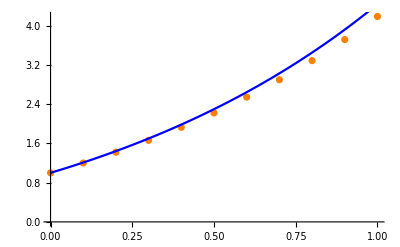

```mathematica
p1 = ListPlot[Table[{x[a,b,n,i],y[a,b,n,i]},{i,0,n}],PlotStyle->Orange];
p2 = Plot[yxact[i],{i,0,1},PlotStyle->Blue];
Show[p1,p2]
```